```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)
(*Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)

MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
KetList[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]

-Graphics-

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],X_0,H_0,X_0,X_1,X_2}

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}],X_0,H_0,X_0,X_1,X_2}

{H_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],H_0}

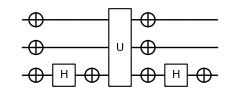

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

-Graphics-

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Toff=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
DrawCircuit[{Toff}]
CCZ=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
CCZCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],Toff,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
ToffCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
CCZClifCirc={Subscript[H, 0],Toff,Subscript[H, 0]}(*{Subscript[X,1],Subscript[X,2],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[X,1],Subscript[X,2]}*)
DrawCircuit[ToffCirc]
CalcCircuitMatrix[{Toff}]//MatrixForm
CalcCircuitMatrix[ToffCirc]//MatrixForm
DrawCircuit[CCZCirc]
CalcCircuitMatrix[{CCZ}] //MatrixForm
CalcCircuitMatrix[CCZCirc] // MatrixForm
CalcCircuitMatrix[CCZClifCirc]//MatrixForm
```

```mathematica
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

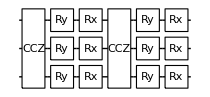
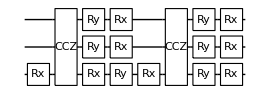
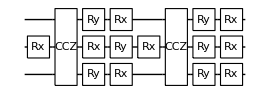
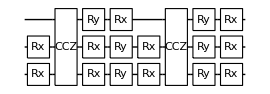
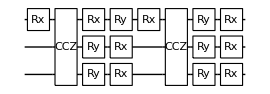
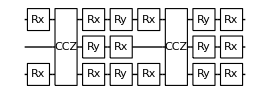
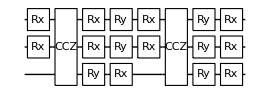
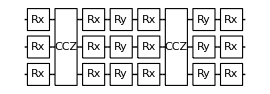

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

{{0.933367,0.00773659,0.00773659,0.00771312,0.00773659,0.00771312,0.00771312,0.00776832},{0.00773795,0.933358,0.00771387,0.00773902,0.00771387,0.00773902,0.00776899,0.00771382},{0.00773795,0.00771387,0.933358,0.00773902,0.00771387,0.00776899,0.00773902,0.00771382},{0.00771367,0.00773771,0.00773771,0.93336,0.0077688,0.00771362,0.00771362,0.00773877},{0.00773795,0.00771387,0.00771387,0.00776899,0.933358,0.00773902,0.00773902,0.00771382},{0.00771367,0.00773771,0.0077688,0.00771362,0.00773771,0.93336,0.00771362,0.00773877},{0.00771367,0.0077688,0.00773771,0.00771362,0.00773771,0.00771362,0.93336,0.00773877},{0.0077685,0.00771333,0.00771333,0.00773682,0.00771333,0.00773682,0.00773682,0.933365}}

```mathematica
InitCirc[NQ_]:=Table[Subscript[Init, b],{b,0,NQ-1,1}]
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed],1]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
Table[DrawCircuit[GroverIteration3Q[KetList[3][[i]]]],{i,1,8}]
KetList[3]
GroversAlg3Q=Table[SearchSeeds=KetList[3];
ρ=CreateDensityQureg[9];
(*InitZeroState[ρ];*)
InitialisationCirc=ExtractCircuit[GetCircuitSchedule[Join[InitCirc[3],HTrans[0],HTrans[1],HTrans[2]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,InitialisationCirc];
Gr=ExtractCircuit[InsertCircuitNoise[GroverIteration3Q[SearchSeeds[[i]]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,Join[Gr,Gr]];CalcProbOfAllOutcomes[ρ,{0,1,2}],{i,1,8}]

DestroyAllQuregs[];
```

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
ToffSandBread[t_,c1_,c2_]:={Subscript[Ry, t][-Pi/2],Subscript[Rx, t][-Pi],Subscript[Rx, c1][Pi],Subscript[Rx, c2][Pi]}
```

```mathematica
Toff[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
CCZGate[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
```

```mathematica
ToffRyd[t_,c1_,c2_]:={{Subscript[X, t],Subscript[X, c1],Subscript[X, c2],Subscript[H, t],Subscript[X, t],CCZGate[t,c1,c2],Subscript[X, t],Subscript[H, t],Subscript[X, t],Subscript[X, c1],Subscript[X, c2]}}
```

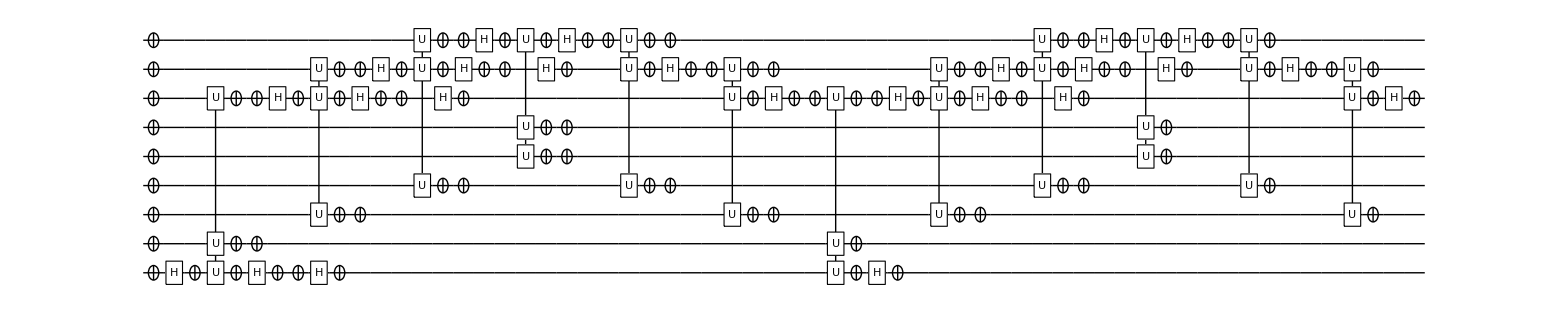

0

```mathematica
(*C4ZMat=DiagonalMatrix[Join[{1},Table[-1,{i,1,2^5-1}]]];
C4XMat=CalcCircuitMatrix[{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]}];
C4XCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4ZCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4XMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4XCircToff={Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2],Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2]};*)
C4XCircCCZ=Flatten[{ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2]}];
DrawCircuit[C4XCircCCZ]
Length[C5ZMat]
```

```mathematica
?Delete
```

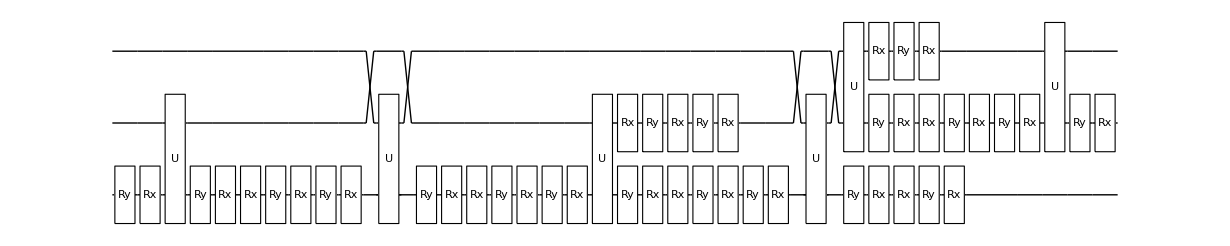

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
HXTrans[q_]:=Subscript[Ry, q][Pi/2]
XHTrans[q_]:=Subscript[Ry, q][-Pi/2]
XHXTrans[q_]:={Subscript[Ry, q][-Pi/2],Subscript[Rx, q][-Pi]}
HXHTrans[q_]:={Subscript[Ry, q][-Pi],Subscript[Rx, q][-Pi]}
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}
Subscript[CCZDecomp,t_,c1_,c2_]:=Flatten[{XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t], Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t],Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],TGate[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1],TGate[c2],Tdg[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1]}]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2],RydDev,ReplaceAliases->True]]]
```

```mathematica
XHXTra
```

```mathematica
KetList[5][[1]][[2;;]]
```

{0,0,0,0}

```mathematica
CliffCCZRyd={HXTrans[0],HXTrans[0],Table[XTrans[i],{i,1,8}],Subscript[CCZ, 0,6,1],HXTrans[6],Subscript[CCZ, 7,6,2],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,5,4] XHTrans[8],Subscript[CCZ, 8,7,3]}
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Join[Position[Reverse[SearchSeed][[1]],1],Position[Reverse[SearchSeed][[2;;]],0]]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
```

```mathematica
?Replace
```

```mathematica
Print[KetList[6][[1]]]
C5XTranspiled=Flatten[{Table[XTrans[i],{i,1,8}],XTrans[0],HXTrans[0],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],,XHTrans[0],XTrans[0],Table[XTrans[i],{i,1,8}]}];
C5ZCliffTrans=Join[HTrans[0],C5XTranspiled,HTrans[0]];
```

{0,0,0,0,0,0}

```mathematica
RenormList2Q=Table[{},{i,1,64}]

GroverOracle6D3A2Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]

GroverDiffusion6D3A2Q=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

GroverAlg6D3A2Q[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q},{j,1,8}]]]

GroverAlg6D3AVaryIt2Q[SearchSeed_]:=Flatten[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q}]
Init9=Table[Subscript[Init, i],{i,0,8}];
GroverDataUnNormCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroverAlg6D3AVaryIt2Q[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList2Q[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,64}]

RenormDataVaryIt2Q=Table[{j,Mean[RenormList2Q[[All,j]]],StandardDeviation[RenormList2Q[[All,j]]]/8},{j,1,8}]
GroverDataUnnormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]/8},{j,1,8}]
GroverData2ndHighestUnnormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]],{i,1,64}]]/8},{j,1,8}]

GroverDataRenormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]/8},{j,1,8}]
GroverData2ndHighestRenormVaryIt2Q=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]]/RenormList2Q[[All,j]][[i]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCZVaryIt[[All,j]][[i]],i]]/RenormList2Q[[All,j]][[i]],{i,1,64}]]/8},{j,1,8}]
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

{{1,0.734217,0.0000469948},{2,0.574485,0.000171744},{3,0.451123,0.000370314},{4,0.355585,0.000560409},{5,0.281647,0.000693049},{6,0.223596,0.000741836},{7,0.177656,0.000719813},{8,0.140988,0.000646049}}

{{1,0.0979423±0.000436605},{2,0.195315±0.00107253},{3,0.258081±0.00161728},{4,0.273696±0.00182908},{5,0.247097±0.00162908},{6,0.195319±0.00115516},{7,0.136402±0.000801417},{8,0.0836495±0.00096609}}

{{1,0.0136792±0.0000945766},{2,0.00787351±0.0000582801},{3,0.00527439±0.0000390548},{4,0.00270932±0.0000366665},{5,0.00168208±0.0000508647},{6,0.00105269±0.0000324545},{7,0.00110444±0.0000195017},{8,0.00133829±0.0000222519}}

{{1,0.133399±0.000600386},{2,0.340015±0.00195702},{3,0.572281±0.00401965},{4,0.770283±0.00622863},{5,0.878387±0.00757872},{6,0.874709±0.00704773},{7,0.768289±0.00471901},{8,0.592366±0.0047116}}

{{1,0.0186306±0.00012806},{2,0.0137066±0.000104096},{3,0.0116924±0.0000877937},{4,0.00761274±0.0000936206},{5,0.00595117±0.000168215},{6,0.00469068±0.000134758},{7,0.00621221±0.000102022},{8,0.00954012±0.000194014}}

{{1,0.265783±0.0000469948},{2,0.425515±0.000171744},{3,0.548877±0.000370314},{4,0.644415±0.000560409},{5,0.718353±0.000693049},{6,0.776404±0.000741836},{7,0.822344±0.000719813},{8,0.859012±0.000646049}}

```mathematica
RenormDataVaryIt2Q={{1,0.7342165303021817,3.5813907106676723*^-9},{2,0.5744849340982545,7.812354455277304*^-9},{3,0.451123347756977,1.1529312939099698*^-8},{4,0.3555850135878708,1.4382338013567163*^-8},{5,0.28164688968026624,1.6822226100152315*^-8},{6,0.22359555509350898,1.9897023196452725*^-8},{7,0.17765624753819118,2.438590391602956*^-8},{8,0.14098756136335625,3.029224370795262*^-8}}
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
```

{{1,0.734217,3.58139×10^-9},{2,0.574485,7.81235×10^-9},{3,0.451123,1.15293×10^-8},{4,0.355585,1.43823×10^-8},{5,0.281647,1.68222×10^-8},{6,0.223596,1.9897×10^-8},{7,0.177656,2.43859×10^-8},{8,0.140988,3.02922×10^-8}}

{{1,0.265783±3.58139×10^-9},{2,0.425515±7.81235×10^-9},{3,0.548877±1.15293×10^-8},{4,0.644415±1.43823×10^-8},{5,0.718353±1.68222×10^-8},{6,0.776404±1.9897×10^-8},{7,0.822344±2.43859×10^-8},{8,0.859012±3.02922×10^-8}}

```mathematica
DestroyAllQuregs[];
```

```mathematica
DestroyAllQuregs[];
```

```mathematica
RenormList=Table[{},{i,1,64}]

(*GroversAlg6D3A[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A},{j,1,8}]]]*)
(*GroverDataUnNormCCZ=Table[If[IntegerQ[i/8],Print[i]];SearchSeed=KetList[6][[i]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3A[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
RenormList[[i]]=Renorm;
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,64}];
*)
RenormList=Table[{},{i,1,64}];
Init9=Table[Subscript[Init, i],{i,0,8}];

GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

GroversAlg6D3AVaryIt[SearchSeed_]:=Flatten[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A}]

GroverDataUnNormCCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3AVaryIt[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,64}];

RenormDataVaryIt=Table[{j,Mean[RenormList[[All,j]]],StandardDeviation[RenormList[[All,j]]]/8},{j,1,8}]
GroverDataUnnormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]/8},{j,1,8}]
GroverData2ndHighestUnnormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]],{i,1,64}]]/8},{j,1,8}]
GroverDataRenormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]/8},{j,1,8}]
GroverData2ndHighestRenormVaryIt=Table[{j,Mean[Table[Max[DeleteDuplicates[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]]/RenormList[[All,j]][[i]],{i,1,64}]]±StandardDeviation[Table[Max[Delete[GroverDataUnNormCCZVaryIt[[All,j]][[i]],i]]/RenormList[[All,j]][[i]],{i,1,64}]]/8},{j,1,8}]
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
(*DrawCircuit[GroverOracle6D3A[KetList[6][[1]]]]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]]*)
(*ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]*)
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
RenormDataVaryIt={{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,3.029224370795262*^-8}}
```

{{1,0.851566,3.58139×10^-9},{2,0.771403,7.81235×10^-9},{3,0.698231,1.15293×10^-8},{4,0.63209,1.43823×10^-8},{5,0.572745,1.68222×10^-8},{6,0.519781,1.9897×10^-8},{7,0.472587,2.43859×10^-8},{8,0.430312,3.02922×10^-8}}

```mathematica
GroverDataUnnormVaryIt={{1,0.11319154796634216±4.1421723588787835*^-8},{2,0.2623050982668577±1.6937839360828093*^-7},{3,0.4087680394945454±3.7074603968770286*^-7},{4,0.5130018601438691±5.938901727411863*^-7},{5,0.5493890716501066±7.63541429789058*^-7},{6,0.5167841648798985±8.256081599218835*^-7},{7,0.4272879232784237±7.495978381192323*^-7},{8,0.30774247560318213±5.580811835102066*^-7}}
```

{{1,0.113192±4.14217×10^-8},{2,0.262305±1.69378×10^-7},{3,0.408768±3.70746×10^-7},{4,0.513002±5.9389×10^-7},{5,0.549389±7.63541×10^-7},{6,0.516784±8.25608×10^-7},{7,0.427288±7.49598×10^-7},{8,0.307742±5.58081×10^-7}}

```mathematica
GroverData2ndHighestUnnormVaryIt={{1,0.011881666450653638±8.498384930656307*^-9},{2,0.00820126822634179±1.7664742446385857*^-8},{3,0.004834604933162689±4.8192509272621464*^-8},{4,0.0020588183523207633±6.354699614885599*^-8},{5,0.0005333542318908827±9.014025347802221*^-8},{6,0.00016060965140730194±1.1263789572844611*^-7},{7,0.0008299895330250968±1.2770863907875202*^-7},{8,0.0020873280462217363±1.5930431779499942*^-7}}
```

{{1,0.0118817±8.49838×10^-9},{2,0.00820127±1.76647×10^-8},{3,0.0048346±4.81925×10^-8},{4,0.00205882±6.3547×10^-8},{5,0.000533354±9.01403×10^-8},{6,0.00016061±1.12638×10^-7},{7,0.00082999±1.27709×10^-7},{8,0.00208733±1.59304×10^-7}}

```mathematica
GroverDataRenormVaryIt={{1,0.13292159178516474±4.8146121522287254*^-8},{2,0.3400362567434216±2.1661012800023092*^-7},{3,0.585434083128625±5.227891823130775*^-7},{4,0.8115957545266411±9.237734559623163*^-7},{5,0.9592218664674655±1.3083864910188895*^-6},{6,0.9942336350669329±1.5539459155519585*^-6},{7,0.9041462935062571±1.5432721011049241*^-6},{8,0.7151610472149355±1.2504886319537253*^-6}}
```

{{1,0.132922±4.81461×10^-8},{2,0.340036±2.1661×10^-7},{3,0.585434±5.22789×10^-7},{4,0.811596±9.23773×10^-7},{5,0.959222±1.30839×10^-6},{6,0.994234±1.55395×10^-6},{7,0.904146±1.54327×10^-6},{8,0.715161±1.25049×10^-6}}

```mathematica
GroverData2ndHighestRenormVartIt={{1,0.013952720375828419±1.00063617074977*^-8},{2,0.010631621598901774±2.2926846787748007*^-8},{3,0.006924079754007015±6.906704410192204*^-8},{4,0.003257158236500212±1.0055483251565255*^-7},{5,0.0009312253705990334±1.573909680040996*^-7},{6,0.0003089946025499827±2.1670615823031924*^-7},{7,0.0017562676574191262±2.702624825540732*^-7},{8,0.004850730172483585±3.704327694138095*^-7}}
```

{{1,0.0139527±1.00064×10^-8},{2,0.0106316±2.29268×10^-8},{3,0.00692408±6.9067×10^-8},{4,0.00325716±1.00555×10^-7},{5,0.000931225±1.57391×10^-7},{6,0.000308995±2.16706×10^-7},{7,0.00175627±2.70262×10^-7},{8,0.00485073±3.70433×10^-7}}

```mathematica
PLossVaryIt={{1,0.14843370105528897±3.5813907106676723*^-9},{2,0.22859667736934408±7.812354455277304*^-9},{3,0.3017693173760526±1.1529312939099698*^-8},{4,0.36790963077134253±1.4382338013567163*^-8},{5,0.4272554756574387±1.6822226100152315*^-8},{6,0.4802185858021687±1.9897023196452725*^-8},{7,0.5274128464109079±2.438590391602956*^-8},{8,0.5696878670903075±3.029224370795262*^-8}}
```

{{1,0.148434±3.58139×10^-9},{2,0.228597±7.81235×10^-9},{3,0.301769±1.15293×10^-8},{4,0.36791±1.43823×10^-8},{5,0.427255±1.68222×10^-8},{6,0.480219±1.9897×10^-8},{7,0.527413±2.43859×10^-8},{8,0.569688±3.02922×10^-8}}

```mathematica
RenormDataVaryIt={{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,0.3029224370795262*^-8}}
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
```

{{1,0.851566,3.58139×10^-9},{2,0.771403,7.81235×10^-9},{3,0.698231,1.15293×10^-8},{4,0.63209,1.43823×10^-8},{5,0.572745,1.68222×10^-8},{6,0.519781,1.9897×10^-8},{7,0.472587,2.43859×10^-8},{8,0.430312,3.02922×10^-9}}

{{1,0.148434±3.58139×10^-9},{2,0.228597±7.81235×10^-9},{3,0.301769±1.15293×10^-8},{4,0.36791±1.43823×10^-8},{5,0.427255±1.68222×10^-8},{6,0.480219±1.9897×10^-8},{7,0.527413±2.43859×10^-8},{8,0.569688±3.02922×10^-9}}

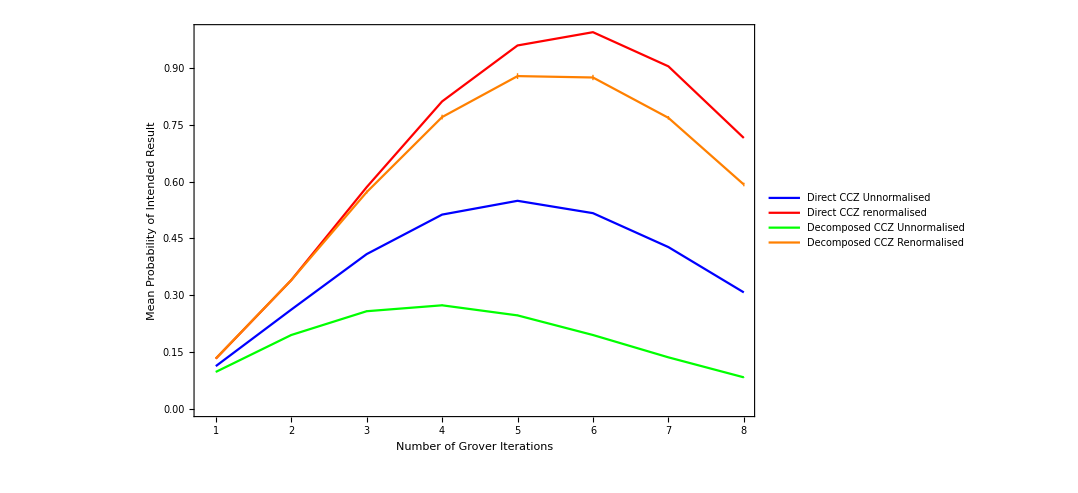

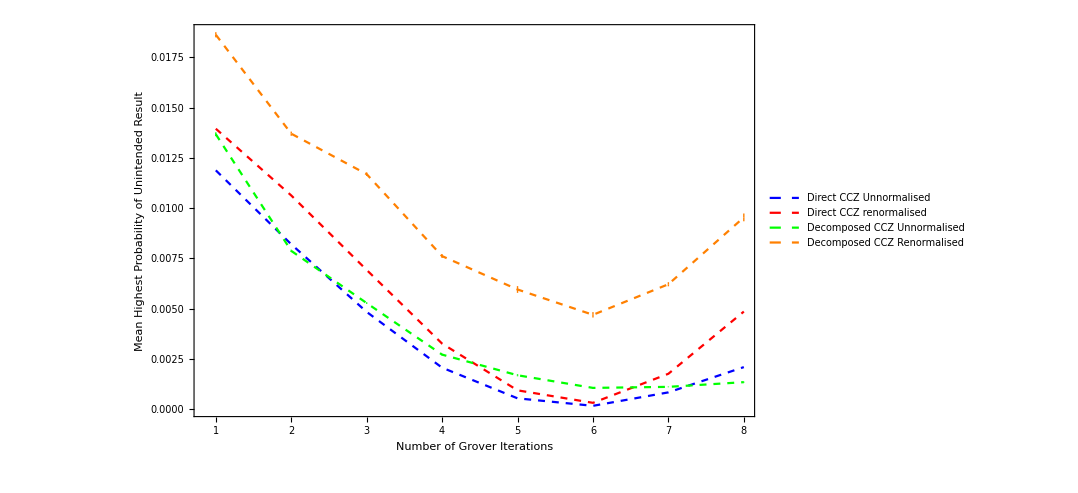

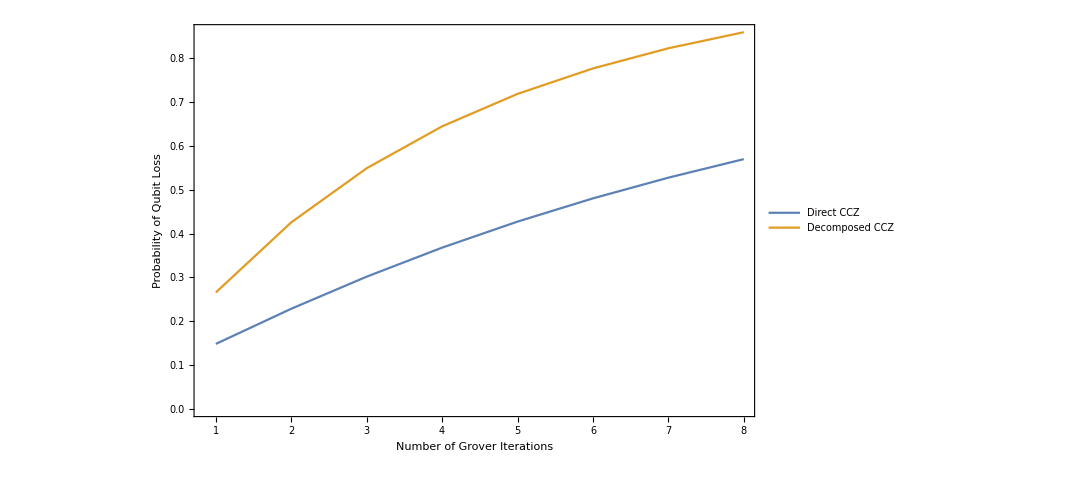

```mathematica
ListLinePlot[{GroverDataUnnormVaryIt,GroverDataRenormVaryIt,GroverDataUnnormVaryIt2Q,GroverDataRenormVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{Blue,Red,Green,Orange},FrameLabel->{"Number of Grover Iterations","Mean Probability of Intended Result"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ Unnormalised","Direct CCZ renormalised","Decomposed CCZ Unnormalised","Decomposed CCZ Renormalised"},{Left,Top}]]
ListLinePlot[{GroverData2ndHighestUnnormVaryIt,GroverData2ndHighestRenormVaryIt,GroverData2ndHighestUnnormVaryIt2Q,GroverData2ndHighestRenormVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Blue,Dashed},{Red,Dashed},{Green,Dashed},{Orange,Dashed}},FrameLabel->{"Number of Grover Iterations"," Mean Highest Probability of Unintended Result"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ Unnormalised","Direct CCZ renormalised","Decomposed CCZ Unnormalised","Decomposed CCZ Renormalised"},{Right,Top}]]
ListLinePlot[{PLossVaryIt,PLossVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],FrameLabel->{"Number of Grover Iterations","Probability of Qubit Loss"},PlotRange->All,PlotLegends->Placed[{"Direct CCZ","Decomposed CCZ"},{Right,Bottom}]]
```

```mathematica
RenormList
```

{0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396}

```mathematica
ρ=CreateQureg[9]

Table[InitZeroState[ρ];InputState=KetList[6][[i]];
XIndices=Position[Reverse[InputState],1];
Xs=Table[Subscript[X,XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
ApplyCircuit[ρ,Xs];
ApplyCircuit[ρ,ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2](*GroverOracle6D3A[InputState[1]]*)(*C5XTranspiled*)(*C5ZTrans*),RydDev,ReplaceAliases->True]]];
(*GetAmp[ρ,i-1,i-1]*)Chop[GetQuregMatrix[ρ][[1;;2^3]]],{i,1,8}]//MatrixForm
(*C5XCircCCZ=Flatten[{Table[HTrans[i],{i,0,5}],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],Table[HTrans[i],{i,0,5}]}];*)
DestroyAllQuregs[];
```

0

(-0.92388-0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ)

```mathematica
?QuEST`*
```

```mathematica
?Round
```

```mathematica
Sqrt[64]
```

```mathematica
CCZDecomp[t_,c1_,c2_]:=
```

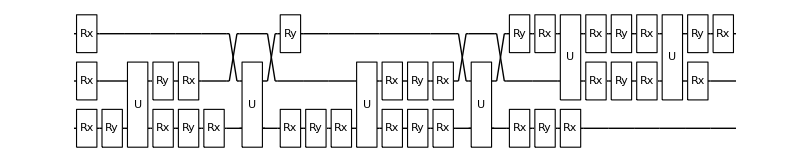

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Rx_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Ry_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

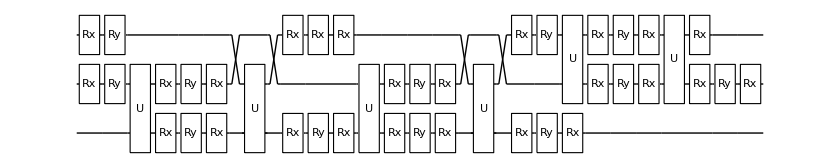

InsertCircuitNoise::error: Encountered gate CZ_(0,1) which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

CalcCircuitMatrix::error: Invalid arguments. See ?CalcCircuitMatrix

```mathematica
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}






{Subscript[Rx, t][-0.09065988720074536],Subscript[Ry, t][-Pi/2],Subscript[Rx, c1][-Pi],Subscript[Rx, c2][-Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.800360109933159],Subscript[Ry, t][1.372292382481866],Subscript[Rx, t][1.63614359593572],Subscript[Ry, c1][-Pi],Subscript[Rx, c1][-Pi],Subscript[CZG, t,c2],Subscript[Rx, t][2.3583],Subscript[Ry, t][0.82493],Subscript[Rx, t][-2.7641],Subscript[Ry, c2][Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.12796],Subscript[Ry, t][0.68257],Subscript[Rx, t][-2.5412],Subscript[Rx, c1][-π/2],Subscript[Ry, c1][Pi/4],Subscript[Rx, c1][-π/2],Subscript[CZG, t,c2],Subscript[Rx, t][-2.7055],Subscript[Ry, t][2.2467],Subscript[Rx, t][2.211],Subscript[Ry, c2][-π/2],Subscript[Rx, c2][Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][π/2],Subscript[Ry, c1][Pi/2],Subscript[Rx, c1][Pi/2],Subscript[Rx, c2][Pi/4],Subscript[Ry, c2][Pi/2],Subscript[Rx, c2][-Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][-Pi],Subscript[Ry, c2][-Pi/4],Subscript[Rx, c2][-Pi/2]};

DrawCircuit[ExtractCircuit[GetCircuitSchedule[CCZDecomp[0,1,2],RydDev,ReplaceAliases->True]]]//MatrixForm
```

```mathematica
?QuEST`*
```

RankedMax[2][{1,2,20},{1,3,50}]

```mathematica
Length[GroverDataUnNormCCZVaryIt[[All,1]][[1]]]
```

64

```mathematica
Length[RenormList[[1]]]
```

8

```mathematica
Table[Correlation[GroverDataUnNormCCZVaryIt[[All,i]],RenormList],{i,1,8}]
```

{{{-0.174036,-0.186384,-0.196619,-0.210033,-0.222576,-0.230057,-0.228719,-0.222934},{0.11243,0.0973153,0.0817994,0.0557915,0.0224533,-0.0147068,-0.0434883,-0.0606285},{-0.149885,-0.166208,-0.180575,-0.196859,-0.209706,-0.213747,-0.206544,-0.194727},{-0.0250758,-0.0340589,-0.049412,-0.0722387,-0.100886,-0.1284,-0.145891,-0.15299},{-0.142027,-0.154269,-0.163237,-0.171641,-0.176128,-0.173172,-0.163196,-0.151668},{0.14444,0.129431,0.115182,0.0941836,0.0689019,0.042178,0.022035,0.0106373},{-0.117875,-0.134093,-0.147193,-0.158467,-0.163257,-0.156863,-0.14102,-0.123462},{0.00693387,-0.00194334,-0.0160297,-0.0338468,-0.0544379,-0.0715155,-0.0803681,-0.0817243},{-0.128458,-0.1371,-0.142331,-0.146156,-0.146223,-0.140638,-0.13059,-0.120654},{0.158009,0.1466,0.136088,0.119669,0.0988065,0.0747129,0.0546422,0.0416528},{-0.104307,-0.116924,-0.126287,-0.132982,-0.133353,-0.124328,-0.108414,-0.0924467},{0.0205024,0.0152259,0.00487656,-0.00836127,-0.0245335,-0.0389809,-0.0477614,-0.0507091},{-0.0964489,-0.104984,-0.108949,-0.107764,-0.099775,-0.0837532,-0.0650663,-0.0493877},{0.190019,0.178716,0.169471,0.158062,0.145255,0.131598,0.120166,0.112919},{-0.0722973,-0.0848085,-0.0929045,-0.0945899,-0.0869048,-0.0674436,-0.0428902,-0.0211806},{0.0525121,0.0473415,0.0382589,0.0300307,0.0219149,0.0179038,0.017762,0.0205568},{-0.182301,-0.176759,-0.171874,-0.171464,-0.174863,-0.181524,-0.187581,-0.192093},{0.104166,0.10694,0.106544,0.09436,0.070167,0.033827,-0.00234911,-0.029787},{-0.158149,-0.156583,-0.15583,-0.15829,-0.161992,-0.165214,-0.165405,-0.163886},{-0.0333403,-0.0244339,-0.0246673,-0.0336701,-0.0531726,-0.0798663,-0.104752,-0.122148},{-0.150291,-0.144644,-0.138492,-0.133073,-0.128414,-0.124639,-0.122058,-0.120828},{0.136176,0.139056,0.139926,0.132752,0.116615,0.0907116,0.063174,0.0414784},{-0.12614,-0.124468,-0.122448,-0.119899,-0.115544,-0.10833,-0.0998819,-0.092621},{-0.00133065,0.00768164,0.00871499,0.00472171,-0.00672439,-0.022982,-0.0392293,-0.0508832},{-0.136723,-0.127475,-0.117586,-0.107587,-0.0985103,-0.092105,-0.0894516,-0.0898132},{0.149744,0.156225,0.160833,0.158238,0.14652,0.123246,0.095781,0.0724938},{-0.112571,-0.107299,-0.101542,-0.0944131,-0.0856398,-0.0757952,-0.0672755,-0.0616062},{0.0122378,0.0248509,0.0296212,0.0302073,0.02318,0.00955258,-0.00662263,-0.0198682},{-0.104713,-0.0953593,-0.0842039,-0.0691957,-0.0520619,-0.0352204,-0.0239284,-0.0185477},{0.181754,0.188341,0.194215,0.19663,0.192969,0.180131,0.161304,0.14376},{-0.0805619,-0.0751835,-0.0681597,-0.0560214,-0.0391915,-0.0189105,-0.00175214,0.00965946},{0.0442475,0.0569665,0.0630036,0.0685991,0.0696283,0.0664371,0.0589005,0.0513973},{-0.182301,-0.176759,-0.171874,-0.171464,-0.174863,-0.181524,-0.187581,-0.192093},{0.104166,0.10694,0.106544,0.09436,0.070167,0.033827,-0.00234911,-0.029787},{-0.158149,-0.156583,-0.15583,-0.15829,-0.161992,-0.165214,-0.165405,-0.163886},{-0.0333403,-0.0244339,-0.0246673,-0.0336701,-0.0531726,-0.0798663,-0.104752,-0.122148},{-0.150291,-0.144644,-0.138492,-0.133073,-0.128414,-0.124639,-0.122058,-0.120828},{0.136176,0.139056,0.139926,0.132752,0.116615,0.0907116,0.063174,0.0414784},{-0.12614,-0.124468,-0.122448,-0.119899,-0.115544,-0.10833,-0.0998819,-0.092621},{-0.00133065,0.00768164,0.00871499,0.00472171,-0.00672439,-0.022982,-0.0392293,-0.0508832},{-0.136723,-0.127475,-0.117586,-0.107587,-0.0985103,-0.092105,-0.0894516,-0.0898132},{0.149744,0.156225,0.160833,0.158238,0.14652,0.123246,0.095781,0.0724938},{-0.112571,-0.107299,-0.101542,-0.0944131,-0.0856398,-0.0757952,-0.0672755,-0.0616062},{0.0122378,0.0248509,0.0296212,0.0302073,0.02318,0.00955258,-0.00662263,-0.0198682},{-0.104713,-0.0953593,-0.0842039,-0.0691957,-0.0520619,-0.0352204,-0.0239284,-0.0185477},{0.181754,0.188341,0.194215,0.19663,0.192969,0.180131,0.161304,0.14376},{-0.0805619,-0.0751835,-0.0681597,-0.0560214,-0.0391915,-0.0189105,-0.00175214,0.00965946},{0.0442475,0.0569665,0.0630036,0.0685991,0.0696283,0.0664371,0.0589005,0.0513973},{-0.0761181,-0.0791005,-0.0766455,-0.0683717,-0.0528929,-0.032823,-0.0136638,-0.000432652},{0.21035,0.2046,0.201774,0.197454,0.192138,0.182529,0.17157,0.161876},{-0.0519664,-0.0589246,-0.0606013,-0.0551975,-0.0400226,-0.0165132,0.00851243,0.0277746},{0.072843,0.0732255,0.0705622,0.0694233,0.0687975,0.0688347,0.0691653,0.0695127},{-0.0441085,-0.046985,-0.0432633,-0.0299798,-0.00644432,0.024062,0.05186,0.0708337},{0.24236,0.236716,0.235157,0.235847,0.238587,0.239414,0.237094,0.233142},{-0.0199567,-0.026809,-0.027219,-0.0168056,0.00642601,0.0403719,0.0740364,0.0990412},{0.104853,0.105341,0.103945,0.107815,0.115246,0.12572,0.134689,0.140779},{-0.03054,-0.0298158,-0.0223571,-0.0044943,0.02346,0.0565966,0.0844668,0.101849},{0.255928,0.253886,0.256064,0.261333,0.268492,0.27195,0.269701,0.264158},{-0.00638823,-0.00963974,-0.00631275,0.00868,0.0363304,0.0729065,0.106643,0.130056},{0.118421,0.122511,0.124851,0.133301,0.145151,0.158255,0.167296,0.171795},{0.00146963,0.0022998,0.0110253,0.0338977,0.0699087,0.113482,0.149991,0.173116},{0.287938,0.286002,0.289446,0.299725,0.314941,0.328835,0.335226,0.335425},{0.0256216,0.0224759,0.0270696,0.047072,0.0827791,0.129792,0.172167,0.201323},{0.150431,0.154626,0.158234,0.171693,0.191599,0.21514,0.23282,0.243061}},{{-0.173863,-0.186595,-0.197156,-0.210896,-0.223688,-0.231258,-0.229828,-0.223868},{0.112104,0.0966465,0.0808189,0.0545028,0.0209225,-0.0163204,-0.0450073,-0.0619713},{-0.150395,-0.167062,-0.181739,-0.198324,-0.211399,-0.2155,-0.208177,-0.196164},{-0.0247982,-0.0341627,-0.0498461,-0.073005,-0.101913,-0.12953,-0.146942,-0.153875},{-0.141924,-0.15455,-0.163848,-0.172589,-0.177342,-0.174499,-0.16445,-0.15276},{0.144043,0.128691,0.114128,0.0928101,0.0672685,0.0404387,0.0203713,0.0091371},{-0.118457,-0.135017,-0.148431,-0.160018,-0.165053,-0.158741,-0.142798,-0.125056},{0.00714077,-0.00211811,-0.0165375,-0.0346979,-0.0555673,-0.0727709,-0.0815636,-0.0827665},{-0.128513,-0.137556,-0.143139,-0.147337,-0.147716,-0.142285,-0.132188,-0.122098},{0.157454,0.145686,0.134837,0.118062,0.0968948,0.0726532,0.0526337,0.0397998},{-0.105045,-0.118023,-0.127722,-0.134766,-0.135427,-0.126527,-0.110536,-0.0943936},{0.0205526,0.0148762,0.00417169,-0.00944619,-0.0259412,-0.0405567,-0.0493016,-0.0521042},{-0.0965737,-0.105512,-0.10983,-0.10903,-0.10137,-0.0855258,-0.0668092,-0.0509892},{0.189394,0.177731,0.168146,0.156369,0.143241,0.129412,0.118013,0.110909},{-0.0731059,-0.0859786,-0.0944132,-0.0964589,-0.0890816,-0.0697683,-0.0451576,-0.0232849},{0.0524916,0.0469209,0.0374803,0.028861,0.0204047,0.0162024,0.0160771,0.0190043},{-0.182949,-0.177173,-0.172118,-0.171632,-0.175085,-0.181949,-0.188283,-0.193043},{0.103017,0.106068,0.105857,0.093767,0.069526,0.0329893,-0.00346144,-0.0311463},{-0.159482,-0.15764,-0.156701,-0.15906,-0.162796,-0.166191,-0.166631,-0.165339},{-0.0338844,-0.0247413,-0.0248075,-0.0337407,-0.0533095,-0.0802201,-0.105396,-0.12305},{-0.15101,-0.145129,-0.138809,-0.133325,-0.128739,-0.12519,-0.122905,-0.121936},{0.134956,0.138113,0.139166,0.132074,0.115872,0.0897482,0.0619169,0.0399617},{-0.127543,-0.125596,-0.123392,-0.120753,-0.11645,-0.109432,-0.101253,-0.0942316},{-0.0019455,0.00730327,0.00850099,0.00456631,-0.00696391,-0.0234615,-0.0400181,-0.051942},{-0.137599,-0.128135,-0.1181,-0.108073,-0.0991133,-0.0929761,-0.0906432,-0.0912737},{0.148368,0.155107,0.159875,0.157326,0.145498,0.121963,0.0941791,0.0706243},{-0.114131,-0.108602,-0.102683,-0.0955017,-0.0868242,-0.0772183,-0.0689915,-0.0635697},{0.0114663,0.0242976,0.0292102,0.029818,0.0226622,0.00875269,-0.00775621,-0.0212797},{-0.10566,-0.0960902,-0.0847919,-0.0697662,-0.0527676,-0.0362172,-0.0252647,-0.0201657},{0.180307,0.187152,0.193184,0.195633,0.191844,0.178722,0.159558,0.141733},{-0.0821922,-0.0765572,-0.0693747,-0.0571948,-0.0404785,-0.0204594,-0.00361294,0.00753861},{0.0434053,0.0563422,0.0625187,0.0681251,0.0690079,0.0655115,0.0576222,0.0498283},{-0.182949,-0.177173,-0.172118,-0.171632,-0.175085,-0.181949,-0.188283,-0.193043},{0.103017,0.106068,0.105857,0.093767,0.069526,0.0329893,-0.00346144,-0.0311463},{-0.159482,-0.15764,-0.156701,-0.15906,-0.162796,-0.166191,-0.166631,-0.165339},{-0.0338844,-0.0247413,-0.0248075,-0.0337407,-0.0533095,-0.0802201,-0.105396,-0.12305},{-0.15101,-0.145129,-0.138809,-0.133325,-0.128739,-0.12519,-0.122905,-0.121936},{0.134956,0.138113,0.139166,0.132074,0.115872,0.0897482,0.0619169,0.0399617},{-0.127543,-0.125596,-0.123392,-0.120753,-0.11645,-0.109432,-0.101253,-0.0942316},{-0.0019455,0.00730327,0.00850099,0.00456631,-0.00696391,-0.0234615,-0.0400181,-0.051942},{-0.137599,-0.128135,-0.1181,-0.108073,-0.0991133,-0.0929761,-0.0906432,-0.0912737},{0.148368,0.155107,0.159875,0.157326,0.145498,0.121963,0.0941791,0.0706243},{-0.114131,-0.108602,-0.102683,-0.0955017,-0.0868242,-0.0772183,-0.0689915,-0.0635697},{0.0114663,0.0242976,0.0292102,0.029818,0.0226622,0.00875269,-0.00775621,-0.0212797},{-0.10566,-0.0960902,-0.0847919,-0.0697662,-0.0527676,-0.0362172,-0.0252647,-0.0201657},{0.180307,0.187152,0.193184,0.195633,0.191844,0.178722,0.159558,0.141733},{-0.0821922,-0.0765572,-0.0693747,-0.0571948,-0.0404785,-0.0204594,-0.00361294,0.00753861},{0.0434053,0.0563422,0.0625187,0.0681251,0.0690079,0.0655115,0.0576222,0.0498283},{-0.0733196,-0.0764347,-0.0739661,-0.0654365,-0.0494556,-0.028736,-0.0090067,0.00459894},{0.212648,0.206808,0.20401,0.199964,0.195157,0.186204,0.175816,0.166498},{-0.0498517,-0.0569015,-0.058549,-0.0528651,-0.0371666,-0.0129782,0.012645,0.0323033},{0.0757458,0.075998,0.0733447,0.072455,0.0723201,0.0729929,0.0738804,0.0745933},{-0.0413807,-0.0443901,-0.0406576,-0.0271294,-0.00310959,0.0280234,0.0563724,0.0757078},{0.244587,0.238853,0.237319,0.238271,0.241503,0.242963,0.241196,0.237607},{-0.0179127,-0.0248569,-0.0252404,-0.014558,0.00917935,0.0437812,0.0780243,0.103412},{0.107685,0.108043,0.106653,0.110762,0.118666,0.129752,0.139259,0.145702},{-0.0279689,-0.0273958,-0.0199485,-0.00187769,0.0265165,0.0602376,0.0886344,0.10637},{0.257999,0.255847,0.258029,0.263523,0.27113,0.275178,0.273458,0.268271},{-0.00450088,-0.00786254,-0.0045312,0.0106938,0.0388055,0.0759954,0.110286,0.134075},{0.121097,0.125037,0.127363,0.136014,0.148292,0.161967,0.171522,0.176365},{0.00397008,0.00464883,0.0133601,0.0364295,0.0728626,0.116997,0.154014,0.17748},{0.289939,0.287893,0.291338,0.301831,0.317476,0.331938,0.338838,0.33938},{0.0274382,0.0241822,0.0287774,0.049001,0.0851516,0.132755,0.175666,0.205184},{0.153036,0.157082,0.160672,0.174321,0.194639,0.218726,0.236901,0.247474}},{{-0.174533,-0.187188,-0.197703,-0.211453,-0.224318,-0.232023,-0.230734,-0.224886},{0.111709,0.0963287,0.0805436,0.0542041,0.0205284,-0.0168813,-0.0457429,-0.0628443},{-0.151098,-0.167689,-0.182323,-0.19892,-0.212066,-0.216295,-0.209104,-0.197195},{-0.0252931,-0.0345775,-0.0502197,-0.0734006,-0.1024,-0.130175,-0.147751,-0.15481},{-0.14234,-0.154888,-0.164129,-0.172841,-0.177603,-0.174811,-0.164834,-0.15321},{0.143903,0.128629,0.114118,0.0928172,0.0672443,0.0403308,0.0201575,0.00883156},{-0.118905,-0.135389,-0.148749,-0.160308,-0.165351,-0.159083,-0.143204,-0.125519},{0.0069007,-0.00227715,-0.0166453,-0.0347879,-0.0556849,-0.0729632,-0.0818506,-0.083135},{-0.128662,-0.137587,-0.143066,-0.147166,-0.147475,-0.142029,-0.131974,-0.121948},{0.15758,0.145931,0.135182,0.118493,0.0973725,0.0731132,0.0530184,0.0400945},{-0.105227,-0.118088,-0.127686,-0.134632,-0.135223,-0.126301,-0.110343,-0.0942566},{0.020578,0.0150241,0.00441785,-0.00911254,-0.0255569,-0.040181,-0.04899,-0.0518723},{-0.0964686,-0.105287,-0.109491,-0.108553,-0.100759,-0.0848168,-0.0660732,-0.0502721},{0.189775,0.178231,0.168756,0.157106,0.144088,0.130326,0.118919,0.111771},{-0.0730336,-0.0857877,-0.0941113,-0.0960196,-0.0885071,-0.0690893,-0.0444428,-0.0225803},{0.052772,0.0473246,0.0379923,0.0295004,0.0211589,0.017031,0.0169105,0.0198037},{-0.183087,-0.177415,-0.172444,-0.172045,-0.175562,-0.182449,-0.188755,-0.193467},{0.103155,0.106102,0.105802,0.0936123,0.0692856,0.0326929,-0.00376266,-0.0314246},{-0.159652,-0.157916,-0.157064,-0.159512,-0.163309,-0.166721,-0.167124,-0.165776},{-0.0338471,-0.0248043,-0.0249611,-0.0339923,-0.0536433,-0.0806009,-0.105771,-0.123391},{-0.150893,-0.145115,-0.13887,-0.133433,-0.128846,-0.125237,-0.122855,-0.121792},{0.135349,0.138402,0.139377,0.132225,0.116001,0.0899048,0.0621375,0.0402509},{-0.127459,-0.125616,-0.12349,-0.120899,-0.116594,-0.10951,-0.101224,-0.0941002},{-0.00165325,0.00749599,0.00861327,0.00462043,-0.00692775,-0.0233892,-0.0398707,-0.0517157},{-0.137216,-0.127814,-0.117807,-0.107757,-0.0987183,-0.0924554,-0.0899945,-0.0905294},{0.149026,0.155704,0.16044,0.157901,0.14613,0.122687,0.0949983,0.0715137},{-0.113781,-0.108315,-0.102427,-0.0952241,-0.0864658,-0.0767277,-0.068364,-0.0628379},{0.0120241,0.0247973,0.0296765,0.0302957,0.0232002,0.00939293,-0.00701013,-0.0204531},{-0.105022,-0.0955139,-0.0842328,-0.0691448,-0.0520027,-0.0352435,-0.0240942,-0.0188538},{0.18122,0.188004,0.194015,0.196514,0.192845,0.179899,0.160899,0.14319},{-0.0815876,-0.0760145,-0.0688526,-0.0566113,-0.0397501,-0.0195157,-0.00246355,0.00883803},{0.044218,0.0570977,0.0632509,0.0689086,0.0699159,0.0666048,0.0588901,0.0512225},{-0.183087,-0.177415,-0.172444,-0.172045,-0.175562,-0.182449,-0.188755,-0.193467},{0.103155,0.106102,0.105802,0.0936123,0.0692856,0.0326929,-0.00376266,-0.0314246},{-0.159652,-0.157916,-0.157064,-0.159512,-0.163309,-0.166721,-0.167124,-0.165776},{-0.0338471,-0.0248043,-0.0249611,-0.0339923,-0.0536433,-0.0806009,-0.105771,-0.123391},{-0.150893,-0.145115,-0.13887,-0.133433,-0.128846,-0.125237,-0.122855,-0.121792},{0.135349,0.138402,0.139377,0.132225,0.116001,0.0899048,0.0621375,0.0402509},{-0.127459,-0.125616,-0.12349,-0.120899,-0.116594,-0.10951,-0.101224,-0.0941002},{-0.00165324,0.00749599,0.00861327,0.00462043,-0.00692775,-0.0233892,-0.0398707,-0.0517157},{-0.137216,-0.127814,-0.117807,-0.107757,-0.0987183,-0.0924554,-0.0899945,-0.0905294},{0.149026,0.155704,0.16044,0.157901,0.14613,0.122687,0.0949983,0.0715137},{-0.113781,-0.108315,-0.102427,-0.0952241,-0.0864658,-0.0767277,-0.068364,-0.0628379},{0.0120241,0.0247973,0.0296765,0.0302957,0.0232002,0.00939293,-0.00701013,-0.0204531},{-0.105022,-0.0955139,-0.0842328,-0.0691448,-0.0520027,-0.0352435,-0.0240942,-0.0188538},{0.18122,0.188004,0.194015,0.196514,0.192845,0.179899,0.160899,0.14319},{-0.0815876,-0.0760145,-0.0688526,-0.0566113,-0.0397501,-0.0195157,-0.00246355,0.00883803},{0.044218,0.0570977,0.0632509,0.0689086,0.0699159,0.0666048,0.0588901,0.0512225},{-0.0743433,-0.0774159,-0.0749461,-0.0665056,-0.0506988,-0.0302129,-0.0106893,0.00277744},{0.2119,0.206103,0.203302,0.199154,0.19415,0.184931,0.174304,0.164822},{-0.0509082,-0.0579164,-0.0595658,-0.0539722,-0.0384463,-0.0144852,0.0109413,0.0304694},{0.0748973,0.0751959,0.0725379,0.071548,0.07122,0.0716356,0.0722952,0.0728541},{-0.0421495,-0.0451156,-0.0413717,-0.0278928,-0.00398289,0.0269995,0.0552116,0.0744539},{0.244094,0.238404,0.236877,0.237767,0.240866,0.242143,0.240206,0.236499},{-0.0187143,-0.025616,-0.0259914,-0.0153593,0.00826967,0.0427273,0.0768425,0.102146},{0.107091,0.107497,0.106113,0.110161,0.117936,0.128848,0.138196,0.144531},{-0.0284722,-0.0278144,-0.0203085,-0.00221749,0.0261451,0.0597817,0.0880722,0.105717},{0.257772,0.255705,0.257941,0.263443,0.270995,0.274926,0.273067,0.267762},{-0.00503692,-0.00831469,-0.00492813,0.0103161,0.0383978,0.0755096,0.109703,0.133409},{0.120769,0.124798,0.127176,0.135837,0.148064,0.16163,0.171057,0.175794},{0.00372174,0.00448607,0.0132659,0.0363955,0.0728612,0.116994,0.153974,0.177394},{0.289966,0.288006,0.291516,0.302056,0.317711,0.332139,0.338969,0.33944},{0.0271571,0.0239859,0.0286464,0.0489291,0.0851139,0.132722,0.175605,0.205086},{0.152963,0.157099,0.160751,0.17445,0.19478,0.218843,0.236958,0.247471}},{{-0.174052,-0.186769,-0.197328,-0.211091,-0.223932,-0.23157,-0.230204,-0.224289},{0.111794,0.0963559,0.0805338,0.0541992,0.0205768,-0.0167264,-0.0454681,-0.0624706},{-0.150647,-0.167295,-0.181967,-0.198573,-0.211694,-0.215863,-0.208602,-0.196634},{-0.0250201,-0.0343707,-0.05005,-0.0732303,-0.102183,-0.129865,-0.147336,-0.154311},{-0.142017,-0.154628,-0.163919,-0.172668,-0.177446,-0.17464,-0.164628,-0.152965},{0.14383,0.128498,0.113944,0.0926225,0.067063,0.0402045,0.0201084,0.00885295},{-0.118612,-0.135153,-0.148558,-0.16015,-0.165208,-0.158932,-0.143026,-0.125311},{0.00701552,-0.00222903,-0.0166406,-0.0348073,-0.0556973,-0.072934,-0.0817599,-0.0829876},{-0.128495,-0.137507,-0.143064,-0.147243,-0.147614,-0.142192,-0.132119,-0.122055},{0.157352,0.145619,0.134798,0.118048,0.0968955,0.0726529,0.052618,0.0397645},{-0.10509,-0.118032,-0.127703,-0.134724,-0.135376,-0.126484,-0.110517,-0.0943997},{0.0205375,0.0148919,0.00421406,-0.0093817,-0.0258651,-0.0404859,-0.0492506,-0.0520765},{-0.0964597,-0.105366,-0.109655,-0.10882,-0.101128,-0.0852611,-0.0665422,-0.0507309},{0.189388,0.177761,0.168208,0.156472,0.143382,0.129584,0.118195,0.111089},{-0.0730545,-0.0858909,-0.0942938,-0.0963015,-0.0888899,-0.0695532,-0.0449397,-0.0230757},{0.0525733,0.0470337,0.0376236,0.0290415,0.0206212,0.0164451,0.0163261,0.0192473},{-0.182943,-0.177202,-0.172177,-0.171728,-0.175216,-0.182105,-0.188446,-0.193201},{0.102903,0.105923,0.105684,0.0935617,0.0692925,0.0327391,-0.00370957,-0.0313829},{-0.159539,-0.157727,-0.156816,-0.15921,-0.162978,-0.166398,-0.166844,-0.165547},{-0.0339111,-0.0248034,-0.0248993,-0.0338676,-0.0534675,-0.0803992,-0.105578,-0.123223},{-0.150908,-0.145061,-0.138768,-0.133305,-0.12873,-0.125175,-0.12287,-0.121879},{0.134939,0.138065,0.139094,0.131985,0.115779,0.0896699,0.0618667,0.0399404},{-0.127503,-0.125586,-0.123407,-0.120787,-0.116492,-0.109467,-0.101268,-0.0942237},{-0.00187553,0.00733823,0.0085101,0.00455543,-0.00698151,-0.0234687,-0.0400015,-0.0519002},{-0.137386,-0.12794,-0.117913,-0.10788,-0.0988982,-0.0927272,-0.0903611,-0.0909678},{0.148461,0.155186,0.159949,0.157411,0.145611,0.122118,0.0943763,0.0708518},{-0.113981,-0.108465,-0.102552,-0.0953617,-0.0866603,-0.0770192,-0.0687587,-0.0633128},{0.0116464,0.0244592,0.0293648,0.029981,0.0228508,0.00897946,-0.00749226,-0.0209891},{-0.105351,-0.0957984,-0.0845043,-0.0694572,-0.0524121,-0.0357964,-0.0247847,-0.0196444},{0.180497,0.187328,0.193359,0.195834,0.192098,0.179049,0.159953,0.142176},{-0.0819457,-0.0763236,-0.0691429,-0.0569387,-0.0401742,-0.0200882,-0.003182,0.00801093},{0.0436822,0.0566009,0.0627743,0.0684042,0.0693369,0.0659103,0.0580842,0.0503344},{-0.182943,-0.177202,-0.172177,-0.171728,-0.175216,-0.182105,-0.188446,-0.193201},{0.102903,0.105923,0.105684,0.0935617,0.0692925,0.0327391,-0.00370957,-0.0313829},{-0.159539,-0.157727,-0.156816,-0.15921,-0.162978,-0.166398,-0.166844,-0.165547},{-0.0339111,-0.0248034,-0.0248993,-0.0338676,-0.0534675,-0.0803992,-0.105578,-0.123223},{-0.150908,-0.145061,-0.138768,-0.133305,-0.12873,-0.125175,-0.12287,-0.121879},{0.134939,0.138065,0.139094,0.131985,0.115779,0.0896699,0.0618667,0.0399404},{-0.127503,-0.125586,-0.123407,-0.120787,-0.116492,-0.109467,-0.101268,-0.0942237},{-0.00187552,0.00733823,0.0085101,0.00455543,-0.00698151,-0.0234687,-0.0400015,-0.0519002},{-0.137386,-0.12794,-0.117913,-0.10788,-0.0988982,-0.0927272,-0.0903611,-0.0909678},{0.148461,0.155186,0.159949,0.157411,0.145611,0.122118,0.0943763,0.0708518},{-0.113981,-0.108465,-0.102552,-0.0953617,-0.0866603,-0.0770192,-0.0687587,-0.0633128},{0.0116464,0.0244592,0.0293648,0.029981,0.0228508,0.00897946,-0.00749226,-0.0209891},{-0.105351,-0.0957984,-0.0845043,-0.0694572,-0.0524121,-0.0357964,-0.0247847,-0.0196444},{0.180497,0.187328,0.193359,0.195834,0.192098,0.179049,0.159953,0.142176},{-0.0819457,-0.0763236,-0.0691429,-0.0569387,-0.0401742,-0.0200882,-0.003182,0.00801093},{0.0436822,0.0566009,0.0627743,0.0684042,0.0693369,0.0659103,0.0580842,0.0503344},{-0.0735354,-0.0766382,-0.0741702,-0.0656698,-0.0497449,-0.0291016,-0.0094406,0.00411809},{0.212312,0.206489,0.203693,0.199622,0.194766,0.185745,0.175298,0.165939},{-0.0501301,-0.0571632,-0.0588088,-0.0531514,-0.0375071,-0.0133936,0.0121622,0.0317736},{0.0754976,0.0757613,0.0731086,0.0721918,0.0720043,0.0726052,0.0734285,0.0740972},{-0.0414998,-0.0444966,-0.0407608,-0.0272467,-0.00325857,0.0278296,0.0561365,0.0754424},{0.244349,0.238631,0.237103,0.238046,0.241252,0.242676,0.240875,0.237264},{-0.0180944,-0.0250215,-0.0253993,-0.0147282,0.00897936,0.0435379,0.0777396,0.103098},{0.107534,0.107903,0.106518,0.110615,0.118491,0.129536,0.139006,0.145422},{-0.0279778,-0.0273757,-0.0199062,-0.00182109,0.0265737,0.0602778,0.0886459,0.106354},{0.257871,0.255752,0.257958,0.263472,0.271085,0.275125,0.273385,0.268176},{-0.00457235,-0.00790048,-0.00454453,0.0106975,0.0388118,0.0759862,0.110249,0.13401},{0.121056,0.125024,0.127373,0.136041,0.148323,0.161985,0.171515,0.176333},{0.00405789,0.00476604,0.0135034,0.0366022,0.0730603,0.117209,0.154224,0.177679},{0.289907,0.287894,0.291369,0.301896,0.317572,0.332057,0.338963,0.339501},{0.0274636,0.0242414,0.0288651,0.0491209,0.0852984,0.132918,0.175827,0.205335},{0.153092,0.157166,0.160783,0.174464,0.19481,0.218917,0.237093,0.247658}},{{-0.174321,-0.187018,-0.197566,-0.211341,-0.224215,-0.231906,-0.230591,-0.224713},{0.111654,0.0962364,0.0804228,0.0540706,0.0204037,-0.0169682,-0.0457775,-0.0628307},{-0.150944,-0.167572,-0.182235,-0.198852,-0.212006,-0.216224,-0.209009,-0.197075},{-0.0251995,-0.0345282,-0.0502001,-0.0733977,-0.102394,-0.13014,-0.147674,-0.154694},{-0.142188,-0.154779,-0.164056,-0.172801,-0.177588,-0.174803,-0.164816,-0.153174},{0.143787,0.128476,0.113934,0.0926104,0.0670309,0.0401352,0.0199977,0.00870904},{-0.118812,-0.135333,-0.148724,-0.160313,-0.165379,-0.159121,-0.143234,-0.125535},{0.00693325,-0.00228915,-0.0166895,-0.0348583,-0.0557669,-0.0730367,-0.0818986,-0.0831547},{-0.128559,-0.137535,-0.143059,-0.147206,-0.147555,-0.142127,-0.132066,-0.122021},{0.157416,0.14572,0.134931,0.118206,0.0970647,0.0728118,0.0527483,0.0398627},{-0.105183,-0.118088,-0.127727,-0.134718,-0.135346,-0.126444,-0.110484,-0.0943817},{0.0205624,0.0149552,0.0043072,-0.00926291,-0.0257333,-0.0403603,-0.0491483,-0.0520013},{-0.0964268,-0.105296,-0.109549,-0.108667,-0.100928,-0.0850238,-0.0662907,-0.0504814},{0.189549,0.17796,0.168442,0.156746,0.143692,0.129916,0.118524,0.111403},{-0.0730502,-0.0858494,-0.0942169,-0.0961784,-0.0887186,-0.0693408,-0.0447081,-0.0228413},{0.0526953,0.0471945,0.037818,0.0292767,0.0208938,0.0167432,0.0166272,0.0195387},{-0.183031,-0.177325,-0.172328,-0.171911,-0.175425,-0.182329,-0.188665,-0.193407},{0.102942,0.105929,0.10566,0.0934997,0.0691934,0.0326098,-0.00385095,-0.031524},{-0.159655,-0.157879,-0.156997,-0.159423,-0.163216,-0.166646,-0.167083,-0.165768},{-0.0339103,-0.0248352,-0.0249625,-0.0339683,-0.0536038,-0.0805616,-0.105747,-0.123387},{-0.150899,-0.145086,-0.138818,-0.133372,-0.128798,-0.125226,-0.12289,-0.121868},{0.135076,0.138169,0.139171,0.13204,0.115821,0.0897132,0.0619241,0.0400154},{-0.127523,-0.12564,-0.123486,-0.120884,-0.116589,-0.109543,-0.101308,-0.0942289},{-0.00177755,0.00740387,0.00854814,0.00457113,-0.00697694,-0.0234586,-0.0399721,-0.0518482},{-0.13727,-0.127842,-0.117821,-0.107777,-0.098765,-0.0925496,-0.0901402,-0.0907154},{0.148705,0.155413,0.160168,0.157635,0.145854,0.12239,0.0946747,0.0711691},{-0.113894,-0.108395,-0.10249,-0.0952883,-0.0865558,-0.0768665,-0.0685577,-0.0630757},{0.0118516,0.0246483,0.0295449,0.0301666,0.0230566,0.00921777,-0.00722178,-0.0206949},{-0.105137,-0.0956029,-0.0843109,-0.0692375,-0.052138,-0.0354462,-0.0243649,-0.0191758},{0.180838,0.187653,0.193679,0.196175,0.192482,0.179494,0.16045,0.142709},{-0.0817611,-0.0761564,-0.0689792,-0.0567488,-0.0399287,-0.0197629,-0.00278207,0.00846437},{0.0439845,0.0568875,0.0630558,0.0687063,0.0696838,0.0663213,0.0585535,0.0508449},{-0.183031,-0.177325,-0.172328,-0.171911,-0.175425,-0.182329,-0.188665,-0.193407},{0.102942,0.105929,0.10566,0.0934997,0.0691934,0.0326098,-0.00385095,-0.031524},{-0.159655,-0.157879,-0.156997,-0.159423,-0.163216,-0.166646,-0.167083,-0.165768},{-0.0339103,-0.0248352,-0.0249625,-0.0339683,-0.0536038,-0.0805616,-0.105747,-0.123387},{-0.150899,-0.145086,-0.138818,-0.133372,-0.128798,-0.125226,-0.12289,-0.121868},{0.135076,0.138169,0.139171,0.13204,0.115821,0.0897132,0.0619241,0.0400154},{-0.127523,-0.12564,-0.123486,-0.120884,-0.116589,-0.109543,-0.101308,-0.0942289},{-0.00177755,0.00740387,0.00854814,0.00457113,-0.00697694,-0.0234586,-0.0399721,-0.0518482},{-0.13727,-0.127842,-0.117821,-0.107777,-0.098765,-0.0925496,-0.0901402,-0.0907154},{0.148705,0.155413,0.160168,0.157635,0.145854,0.12239,0.0946747,0.0711691},{-0.113894,-0.108395,-0.10249,-0.0952883,-0.0865558,-0.0768665,-0.0685577,-0.0630757},{0.0118516,0.0246483,0.0295449,0.0301666,0.0230566,0.00921777,-0.00722178,-0.0206949},{-0.105137,-0.0956029,-0.0843109,-0.0692375,-0.052138,-0.0354462,-0.0243649,-0.0191758},{0.180838,0.187653,0.193679,0.196175,0.192482,0.179494,0.16045,0.142709},{-0.0817611,-0.0761564,-0.0689792,-0.0567488,-0.0399287,-0.0197629,-0.00278207,0.00846437},{0.0439845,0.0568875,0.0630558,0.0687063,0.0696838,0.0663213,0.0585535,0.0508449},{-0.0738829,-0.0769734,-0.0745052,-0.0660341,-0.0501651,-0.0295969,-0.0100012,0.00351341},{0.212093,0.206283,0.203486,0.199379,0.194456,0.185344,0.174815,0.165399},{-0.0505062,-0.0575267,-0.0591734,-0.0535452,-0.0379557,-0.0139135,0.0115817,0.0311538},{0.0752392,0.0755172,0.0728616,0.0719099,0.0716569,0.0721708,0.0729174,0.0735344},{-0.0417502,-0.0447344,-0.0409946,-0.0274945,-0.00353782,0.0275071,0.0557748,0.075054},{0.244226,0.238523,0.236997,0.23792,0.241083,0.242448,0.240591,0.236941},{-0.0183733,-0.0252875,-0.0256626,-0.0150055,0.0086717,0.0431906,0.0773581,0.102695},{0.107372,0.107757,0.106373,0.11045,0.118284,0.129275,0.138693,0.145075},{-0.0281211,-0.02749,-0.0199979,-0.00189902,0.0264958,0.0601835,0.0885252,0.106208},{0.257856,0.255767,0.257994,0.263515,0.271117,0.275125,0.273342,0.268095},{-0.00474404,-0.00804296,-0.00466569,0.0105901,0.0387055,0.0758672,0.110109,0.133849},{0.121002,0.125001,0.12737,0.136046,0.148318,0.161951,0.171444,0.176229},{0.0040118,0.00474917,0.013513,0.0366408,0.0731234,0.117288,0.154302,0.177749},{0.289989,0.288007,0.291506,0.302056,0.317746,0.33223,0.339119,0.339636},{0.0273891,0.0241965,0.0288453,0.04913,0.0853332,0.132972,0.175886,0.20539},{0.153135,0.157241,0.160881,0.174586,0.194946,0.219056,0.237221,0.24777}},{{-0.174204,-0.186906,-0.197459,-0.211237,-0.224112,-0.231802,-0.230484,-0.224604},{0.11157,0.0961498,0.080335,0.0539888,0.0203357,-0.0170139,-0.0457999,-0.0628346},{-0.150845,-0.167475,-0.18214,-0.198758,-0.211913,-0.216131,-0.208918,-0.196986},{-0.0251867,-0.0345228,-0.0501961,-0.0733899,-0.102375,-0.130106,-0.147624,-0.154633},{-0.142093,-0.154689,-0.163971,-0.172723,-0.177516,-0.174736,-0.164753,-0.153112},{0.143682,0.128368,0.113824,0.0925033,0.0669322,0.0400519,0.0199319,0.00865791},{-0.118734,-0.135257,-0.148652,-0.160245,-0.165317,-0.159066,-0.143187,-0.125493},{0.00692487,-0.00230496,-0.0167075,-0.0348759,-0.0557793,-0.0730405,-0.0818927,-0.0831412},{-0.128487,-0.137471,-0.143005,-0.147165,-0.147526,-0.14211,-0.132055,-0.122011},{0.157288,0.145586,0.13479,0.118062,0.0969224,0.0726791,0.0526305,0.0397593},{-0.105128,-0.11804,-0.127686,-0.134686,-0.135327,-0.126439,-0.110488,-0.094392},{0.0205308,0.0149127,0.00425847,-0.00931717,-0.0257893,-0.0404134,-0.0491944,-0.0520401},{-0.096376,-0.105254,-0.109517,-0.108651,-0.10093,-0.0850439,-0.0663226,-0.0505187},{0.1894,0.177804,0.168279,0.156577,0.143519,0.129745,0.118363,0.111253},{-0.0730166,-0.0858218,-0.0941971,-0.0961719,-0.0887302,-0.0693726,-0.0447558,-0.0228986},{0.0526427,0.0471308,0.0377473,0.0291972,0.0208072,0.0166525,0.0165377,0.0194528},{-0.182939,-0.177226,-0.172226,-0.171806,-0.17532,-0.182226,-0.188568,-0.193317},{0.102835,0.105829,0.105568,0.093419,0.0691278,0.032562,-0.00388391,-0.0315472},{-0.15958,-0.157795,-0.156907,-0.159328,-0.16312,-0.166555,-0.167003,-0.165698},{-0.0339213,-0.0248427,-0.024963,-0.0339593,-0.053583,-0.0805298,-0.105708,-0.123346},{-0.150828,-0.145009,-0.138738,-0.133293,-0.128724,-0.125161,-0.122837,-0.121825},{0.134947,0.138048,0.139057,0.131934,0.115724,0.0896278,0.0618479,0.0399451},{-0.127469,-0.125577,-0.123418,-0.120814,-0.116524,-0.10949,-0.101271,-0.0942061},{-0.00180974,0.00737517,0.00852557,0.00455481,-0.00698687,-0.0234643,-0.0399767,-0.0518538},{-0.137222,-0.127791,-0.117772,-0.107734,-0.0987338,-0.092534,-0.0901392,-0.0907247},{0.148553,0.155266,0.160023,0.157492,0.145715,0.122255,0.0945464,0.0710464},{-0.113863,-0.108359,-0.102452,-0.0952552,-0.0865341,-0.0768628,-0.0685726,-0.0631051},{0.0117963,0.0245929,0.0294916,0.0301136,0.0230032,0.00916274,-0.00727837,-0.0207528},{-0.10511,-0.0955737,-0.0842839,-0.0692201,-0.0521376,-0.0354682,-0.0244072,-0.0192321},{0.180665,0.187484,0.193512,0.196007,0.192312,0.179321,0.160279,0.14254},{-0.0817514,-0.0761417,-0.0689638,-0.056741,-0.0399376,-0.0197966,-0.00284014,0.00838807},{0.0439081,0.056811,0.0629805,0.068628,0.0695998,0.0662287,0.0584537,0.05074},{-0.182939,-0.177226,-0.172226,-0.171806,-0.17532,-0.182226,-0.188568,-0.193317},{0.102835,0.105829,0.105568,0.093419,0.0691278,0.032562,-0.00388391,-0.0315472},{-0.15958,-0.157795,-0.156907,-0.159328,-0.16312,-0.166555,-0.167003,-0.165698},{-0.0339213,-0.0248427,-0.024963,-0.0339593,-0.053583,-0.0805298,-0.105708,-0.123346},{-0.150828,-0.145009,-0.138738,-0.133293,-0.128724,-0.125161,-0.122837,-0.121825},{0.134947,0.138048,0.139057,0.131934,0.115724,0.0896278,0.0618479,0.0399451},{-0.127469,-0.125577,-0.123418,-0.120814,-0.116524,-0.10949,-0.101271,-0.0942061},{-0.00180973,0.00737517,0.00852557,0.00455481,-0.00698687,-0.0234643,-0.0399767,-0.0518538},{-0.137222,-0.127791,-0.117772,-0.107734,-0.0987338,-0.092534,-0.0901392,-0.0907247},{0.148553,0.155266,0.160023,0.157492,0.145715,0.122255,0.0945464,0.0710464},{-0.113863,-0.108359,-0.102452,-0.0952552,-0.0865341,-0.0768628,-0.0685726,-0.0631051},{0.0117963,0.0245929,0.0294916,0.0301136,0.0230032,0.00916274,-0.00727837,-0.0207528},{-0.10511,-0.0955737,-0.0842839,-0.0692201,-0.0521376,-0.0354682,-0.0244072,-0.0192321},{0.180665,0.187484,0.193512,0.196007,0.192312,0.179321,0.160279,0.14254},{-0.0817514,-0.0761417,-0.0689638,-0.056741,-0.0399376,-0.0197966,-0.00284014,0.00838807},{0.0439081,0.056811,0.0629805,0.068628,0.0695998,0.0662287,0.0584537,0.05074},{-0.0737336,-0.0768259,-0.0743584,-0.0658826,-0.0500049,-0.0294257,-0.00982174,0.00369784},{0.212043,0.206233,0.203438,0.199346,0.194445,0.185365,0.174865,0.165471},{-0.0503741,-0.0573936,-0.059038,-0.0534033,-0.0378049,-0.013754,0.0117455,0.0313183},{0.0752851,0.075559,0.0729063,0.0719658,0.0717326,0.0722713,0.0730394,0.0736703},{-0.0416221,-0.0446082,-0.0408698,-0.0273683,-0.00340829,0.0276407,0.0559111,0.0751915},{0.244155,0.238451,0.236928,0.237861,0.241042,0.242432,0.240598,0.236965},{-0.0182622,-0.0251756,-0.0255492,-0.0148888,0.00879202,0.0433127,0.0774788,0.102813},{0.107397,0.107777,0.106395,0.11048,0.11833,0.129338,0.138772,0.145164},{-0.028016,-0.0273904,-0.0199037,-0.00180955,0.0265819,0.0602678,0.0886095,0.106293},{0.257761,0.255669,0.257894,0.26342,0.271033,0.275059,0.273297,0.268067},{-0.00465611,-0.00795766,-0.00458298,0.0106701,0.0387824,0.0759401,0.110177,0.133914},{0.121003,0.124995,0.127362,0.136039,0.14832,0.161965,0.171471,0.176266},{0.00409577,0.00482764,0.0135851,0.036705,0.0731789,0.117335,0.154343,0.177787},{0.289874,0.287888,0.291384,0.301935,0.317631,0.332127,0.339031,0.339562},{0.027456,0.0242607,0.0289061,0.0491849,0.0853797,0.133007,0.175911,0.205409},{0.153116,0.157214,0.160851,0.174554,0.194917,0.219033,0.237205,0.24776}},{{-0.17396,-0.186674,-0.197232,-0.210992,-0.22383,-0.231468,-0.230103,-0.224189},{0.111719,0.0962843,0.0804665,0.0541419,0.0205349,-0.0167481,-0.0454717,-0.0624614},{-0.15055,-0.167193,-0.181862,-0.198464,-0.211584,-0.215755,-0.208499,-0.196538},{-0.025026,-0.0343761,-0.0500507,-0.0732222,-0.102162,-0.129829,-0.147289,-0.154257},{-0.141947,-0.154556,-0.163846,-0.172596,-0.177377,-0.174577,-0.164572,-0.152915},{0.143733,0.128404,0.113853,0.0925391,0.0669894,0.0401437,0.0200597,0.00881304},{-0.118536,-0.135074,-0.148476,-0.160068,-0.16513,-0.158863,-0.142968,-0.125263},{0.00698764,-0.0022565,-0.0166643,-0.0348257,-0.0557084,-0.0729378,-0.0817583,-0.0829833},{-0.128408,-0.137418,-0.142974,-0.147151,-0.147521,-0.142099,-0.132028,-0.121966},{0.157273,0.145542,0.134726,0.117985,0.0968461,0.0726222,0.0526045,0.0397632},{-0.104997,-0.117936,-0.127603,-0.134622,-0.135273,-0.126385,-0.110424,-0.0943134},{0.020527,0.0148816,0.00420791,-0.00938009,-0.0258518,-0.0404595,-0.0492137,-0.0520334},{-0.0963947,-0.105299,-0.109588,-0.108754,-0.101067,-0.0852073,-0.0664961,-0.050691},{0.189287,0.177663,0.168113,0.156382,0.143301,0.129515,0.118137,0.111039},{-0.0729833,-0.0858162,-0.0942171,-0.0962257,-0.088819,-0.0694925,-0.0448912,-0.0230378},{0.0525411,0.0470015,0.0375947,0.0290169,0.0206027,0.0164326,0.0163182,0.0192417},{-0.182863,-0.177122,-0.172099,-0.171652,-0.175142,-0.182033,-0.188377,-0.193134},{0.102816,0.105836,0.105599,0.093482,0.0692236,0.0326867,-0.00374529,-0.0314057},{-0.159453,-0.157641,-0.156729,-0.159124,-0.162895,-0.16632,-0.166773,-0.165482},{-0.0339286,-0.0248235,-0.0249179,-0.0338817,-0.0534732,-0.080394,-0.105563,-0.123201},{-0.15085,-0.145003,-0.138713,-0.133256,-0.128688,-0.125142,-0.122846,-0.12186},{0.13483,0.137957,0.138986,0.131879,0.115678,0.0895786,0.0617862,0.0398688},{-0.127439,-0.125521,-0.123343,-0.120727,-0.116441,-0.109428,-0.101242,-0.0942078},{-0.00191492,0.0072962,0.00846868,0.00451506,-0.00701902,-0.0235025,-0.0400315,-0.0519273},{-0.13731,-0.127865,-0.117841,-0.10781,-0.0988316,-0.0926642,-0.0903015,-0.0909103},{0.14837,0.155095,0.159858,0.157325,0.145535,0.122057,0.094331,0.0708189},{-0.1139,-0.108383,-0.10247,-0.0952814,-0.0865839,-0.0769495,-0.068697,-0.0632579},{0.0116245,0.0244343,0.029341,0.0299608,0.0228377,0.00897588,-0.00748687,-0.0209774},{-0.105297,-0.0957455,-0.0844546,-0.0694135,-0.0523773,-0.0357722,-0.0247698,-0.0196355},{0.180384,0.187215,0.193246,0.195723,0.19199,0.17895,0.159863,0.142094},{-0.0818861,-0.0762635,-0.0690839,-0.0568845,-0.0401293,-0.0200571,-0.00316462,0.00801776},{0.0436386,0.0565544,0.0627279,0.068358,0.0692924,0.0658681,0.0580451,0.0502977},{-0.182863,-0.177122,-0.172099,-0.171652,-0.175142,-0.182033,-0.188377,-0.193134},{0.102816,0.105836,0.105599,0.093482,0.0692236,0.0326867,-0.00374529,-0.0314057},{-0.159453,-0.157641,-0.156729,-0.159124,-0.162895,-0.16632,-0.166773,-0.165482},{-0.0339286,-0.0248235,-0.0249179,-0.0338817,-0.0534732,-0.080394,-0.105563,-0.123201},{-0.15085,-0.145003,-0.138713,-0.133256,-0.128688,-0.125142,-0.122846,-0.12186},{0.13483,0.137957,0.138986,0.131879,0.115678,0.0895786,0.0617862,0.0398688},{-0.127439,-0.125521,-0.123343,-0.120727,-0.116441,-0.109428,-0.101242,-0.0942078},{-0.00191492,0.0072962,0.00846868,0.00451506,-0.00701902,-0.0235025,-0.0400315,-0.0519273},{-0.13731,-0.127865,-0.117841,-0.10781,-0.0988316,-0.0926642,-0.0903015,-0.0909103},{0.14837,0.155095,0.159858,0.157325,0.145535,0.122057,0.094331,0.0708189},{-0.1139,-0.108383,-0.10247,-0.0952814,-0.0865839,-0.0769495,-0.068697,-0.0632579},{0.0116245,0.0244343,0.029341,0.0299608,0.0228377,0.00897588,-0.00748687,-0.0209774},{-0.105297,-0.0957455,-0.0844546,-0.0694135,-0.0523773,-0.0357722,-0.0247698,-0.0196355},{0.180384,0.187215,0.193246,0.195723,0.19199,0.17895,0.159863,0.142094},{-0.0818861,-0.0762635,-0.0690839,-0.0568845,-0.0401293,-0.0200571,-0.00316462,0.00801776},{0.0436386,0.0565544,0.0627279,0.068358,0.0692924,0.0658681,0.0580451,0.0502977},{-0.0734793,-0.0765827,-0.0741179,-0.0656227,-0.0497055,-0.0290709,-0.00941725,0.00413689},{0.212203,0.206379,0.203583,0.199514,0.194663,0.185652,0.175217,0.165868},{-0.0500677,-0.0571002,-0.0587468,-0.0530935,-0.0374574,-0.0133555,0.0121882,0.0317907},{0.0754565,0.0757174,0.0730648,0.0721489,0.0719643,0.0725696,0.0733978,0.0740704},{-0.0414657,-0.0444632,-0.0407314,-0.0272259,-0.00325086,0.0278217,0.0561154,0.0754129},{0.244218,0.2385,0.236971,0.237913,0.241119,0.242545,0.24075,0.237145},{-0.0180536,-0.0249802,-0.02536,-0.0146963,0.0089977,0.0435376,0.0777216,0.103068},{0.107471,0.107838,0.106452,0.110546,0.118419,0.129463,0.138931,0.145347},{-0.0279262,-0.027325,-0.0198591,-0.00178009,0.0266059,0.0603003,0.0886602,0.106363},{0.257757,0.255638,0.257844,0.263359,0.270976,0.275024,0.273295,0.268095},{-0.00451401,-0.00784185,-0.00448741,0.0107497,0.0388548,0.0760165,0.110267,0.134018},{0.12101,0.124976,0.127325,0.135992,0.148276,0.161941,0.171476,0.176297},{0.00408785,0.00479499,0.0135278,0.0366172,0.0730612,0.117194,0.154194,0.17764},{0.289773,0.28776,0.291232,0.301757,0.317432,0.331918,0.33883,0.339373},{0.0275004,0.0242785,0.0288998,0.0491474,0.0853104,0.13291,0.175801,0.205296},{0.153025,0.157097,0.160712,0.17439,0.194732,0.218835,0.23701,0.247575}},{{-0.174532,-0.187205,-0.197744,-0.211544,-0.224475,-0.232253,-0.23102,-0.225203},{0.111242,0.095856,0.0800557,0.0536874,0.019974,-0.0174693,-0.0463467,-0.0634495},{-0.15126,-0.167855,-0.182505,-0.199143,-0.212351,-0.216653,-0.20952,-0.197646},{-0.0254663,-0.0347719,-0.0504331,-0.0736515,-0.102699,-0.130524,-0.148133,-0.155209},{-0.142272,-0.154839,-0.164101,-0.172851,-0.177663,-0.174922,-0.164983,-0.153379},{0.143504,0.128225,0.113701,0.0923814,0.0667876,0.0398621,0.019691,0.00837569},{-0.118999,-0.135488,-0.148861,-0.16045,-0.165538,-0.159322,-0.143482,-0.12582},{0.00679484,-0.00240406,-0.0167886,-0.0349583,-0.055886,-0.0731927,-0.0820956,-0.0833845},{-0.128519,-0.13745,-0.142938,-0.147056,-0.147393,-0.141979,-0.131952,-0.121945},{0.157257,0.145613,0.134864,0.118177,0.0970578,0.0728057,0.0527222,0.0398099},{-0.105246,-0.118099,-0.127698,-0.134655,-0.135268,-0.126378,-0.110451,-0.0943862},{0.020548,0.0149845,0.00437488,-0.00916309,-0.0256158,-0.0402493,-0.0490646,-0.0519504},{-0.0962589,-0.105083,-0.109294,-0.108363,-0.10058,-0.0846478,-0.0659142,-0.0501192},{0.189519,0.177982,0.16851,0.156871,0.143872,0.130138,0.118761,0.111637},{-0.0729845,-0.0857313,-0.0940533,-0.0959614,-0.0884545,-0.0690461,-0.0444118,-0.0225592},{0.0528097,0.0473528,0.0380199,0.0295308,0.0211979,0.0170827,0.016974,0.0198757},{-0.182984,-0.177325,-0.17237,-0.172002,-0.175559,-0.182492,-0.188833,-0.193566},{0.10279,0.105735,0.105429,0.0932283,0.0688897,0.0322913,-0.00415961,-0.0318122},{-0.159711,-0.157975,-0.157131,-0.159601,-0.163435,-0.166892,-0.167333,-0.166008},{-0.0339174,-0.0248918,-0.0250591,-0.0341099,-0.0537824,-0.0807624,-0.105945,-0.123571},{-0.150723,-0.144958,-0.138727,-0.133309,-0.128746,-0.125161,-0.122796,-0.121741},{0.135052,0.138104,0.139074,0.131923,0.115704,0.0896232,0.0618785,0.0400132},{-0.127451,-0.125608,-0.123487,-0.120908,-0.116621,-0.10956,-0.101294,-0.0941828},{-0.00165622,0.00747624,0.00858562,0.00458369,-0.00696914,-0.0234311,-0.0399077,-0.0517464},{-0.13697,-0.12757,-0.117563,-0.107514,-0.0984762,-0.0922179,-0.0897647,-0.0903074},{0.148805,0.155493,0.160238,0.157718,0.145974,0.122567,0.0949098,0.0714475},{-0.113697,-0.108219,-0.102323,-0.0951126,-0.086351,-0.0766165,-0.0682631,-0.0627485},{0.0120971,0.0248649,0.0297493,0.0303791,0.0233012,0.00951255,-0.00687644,-0.0203123},{-0.10471,-0.0952022,-0.0839192,-0.0688209,-0.0516628,-0.0348861,-0.0237263,-0.0184815},{0.181068,0.187862,0.193884,0.196413,0.192789,0.1799,0.160949,0.143274},{-0.081436,-0.075851,-0.0686787,-0.0564188,-0.039537,-0.0192839,-0.00222358,0.00907864},{0.0443588,0.0572335,0.0633946,0.0690734,0.0701153,0.0668449,0.0591624,0.0515141},{-0.182984,-0.177325,-0.17237,-0.172002,-0.175559,-0.182492,-0.188833,-0.193566},{0.10279,0.105735,0.105429,0.0932283,0.0688897,0.0322913,-0.00415961,-0.0318122},{-0.159711,-0.157975,-0.157131,-0.159601,-0.163435,-0.166892,-0.167333,-0.166008},{-0.0339174,-0.0248918,-0.0250591,-0.0341099,-0.0537824,-0.0807624,-0.105945,-0.123571},{-0.150723,-0.144958,-0.138727,-0.133309,-0.128746,-0.125161,-0.122796,-0.121741},{0.135052,0.138104,0.139074,0.131923,0.115704,0.0896232,0.0618785,0.0400132},{-0.127451,-0.125608,-0.123487,-0.120908,-0.116621,-0.10956,-0.101294,-0.0941828},{-0.00165621,0.00747624,0.00858562,0.00458369,-0.00696914,-0.0234311,-0.0399077,-0.0517464},{-0.13697,-0.12757,-0.117563,-0.107514,-0.0984762,-0.0922179,-0.0897647,-0.0903074},{0.148805,0.155493,0.160238,0.157718,0.145974,0.122567,0.0949098,0.0714475},{-0.113697,-0.108219,-0.102323,-0.0951126,-0.086351,-0.0766165,-0.0682631,-0.0627485},{0.0120971,0.0248649,0.0297493,0.0303791,0.0233012,0.00951255,-0.00687644,-0.0203123},{-0.10471,-0.0952022,-0.0839192,-0.0688209,-0.0516628,-0.0348861,-0.0237263,-0.0184815},{0.181068,0.187862,0.193884,0.196413,0.192789,0.1799,0.160949,0.143274},{-0.081436,-0.075851,-0.0686787,-0.0564188,-0.039537,-0.0192839,-0.00222358,0.00907864},{0.0443588,0.0572335,0.0633946,0.0690734,0.0701153,0.0668449,0.0591624,0.0515141},{-0.0741732,-0.0772466,-0.0747795,-0.0663497,-0.05056,-0.0300996,-0.0106004,0.00284781},{0.211605,0.205819,0.203025,0.198885,0.193893,0.184687,0.174076,0.164605},{-0.0508985,-0.0578947,-0.0595384,-0.0539471,-0.0384338,-0.014497,0.0109028,0.0304087},{0.0748953,0.0751892,0.0725344,0.0715448,0.0712183,0.0716316,0.0722885,0.0728437},{-0.0419121,-0.0448788,-0.0411349,-0.027656,-0.00374611,0.027233,0.0554391,0.0746751},{0.243868,0.238188,0.236671,0.237581,0.240708,0.242021,0.240116,0.236433},{-0.0186368,-0.0255262,-0.0258933,-0.0152528,0.00838071,0.0428364,0.0769434,0.102237},{0.107158,0.107558,0.10618,0.110239,0.118033,0.128965,0.138328,0.144671},{-0.0281587,-0.0274901,-0.0199712,-0.00186045,0.0265244,0.0601769,0.0884705,0.10611},{0.257621,0.255577,0.257835,0.263376,0.270979,0.274965,0.273148,0.267868},{-0.00488327,-0.00813726,-0.00472925,0.010543,0.0386516,0.0757807,0.109975,0.133672},{0.120911,0.124947,0.127344,0.136035,0.148304,0.161909,0.17136,0.176106},{0.00410291,0.00487834,0.013674,0.036834,0.0733391,0.117511,0.154511,0.177938},{0.289885,0.287948,0.291482,0.302073,0.317795,0.3323,0.33919,0.339698},{0.027379,0.0242317,0.0289165,0.049238,0.085467,0.133115,0.176017,0.205502},{0.153174,0.157317,0.16099,0.174731,0.195119,0.219243,0.237401,0.247935}}}

```mathematica
1]
```

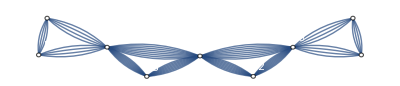

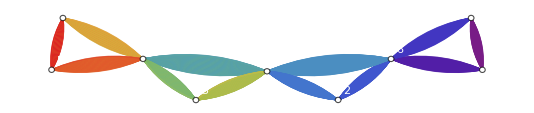

```mathematica
GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

GroversAlg6D3AVaryIt[SearchSeed_]:=Flatten[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A}]

GroverOracle6D3A2Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]

GroverDiffusion6D3A2Q=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

GroverAlg6D3A2Q[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q},{j,1,8}]]]

DrawCircuitTopology[GroversAlg6D3AVaryIt[KetList[6][[1]]],ShowLocalGates->False, ShowRepetitions->True,DistinguishBy->CCZ]
DrawCircuitTopology[GroverAlg6D3A2Q[KetList[6][[1]]],ShowLocalGates->False, ShowRepetitions->True,DistinguishBy->CZ]
```

```mathematica
?DrawCircuitTopology
```